```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/csv_outputs/quadratic.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

```mathematica
"
```

0.180885+0.000151361 words-2.43924×10^-10 words^2

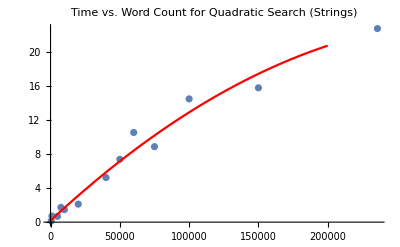

Set::write: Tag List in {762, 7329, 73227, 109472, 14682, 172484, 29256, 397, 3691, 36460, 43964, 5547, 54874}[words_] is Protected.

37.3114+0.730786 words

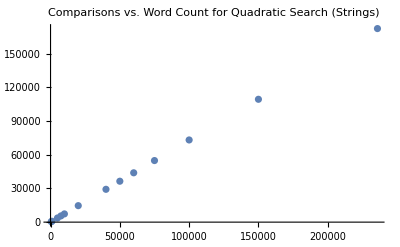

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Quadratic Search (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Quadratic Search (Strings)"]
```

```mathematica
"
```